```mathematica
ClearAll;
```

```mathematica
Action = (((r*Sin[θ[r]])^2)*((1+(r^2))^(-1)+((r*(θ'[r]))^2)))^(1/2)
```

√(r^2 Sin[θ[r]]^2 (1/(1+r^2)+r^2 θ'[r]^2))

```mathematica
RHSr = FullSimplify[D[Action,θ[r]]]; (*Compute Euler Lagrange Equations*)
```

```mathematica
LHSr=FullSimplify[Dt[D[Action,θ'[r]],r]];
```

```mathematica
r0j=4;
Jointed = NDSolve[{RHSr==LHSr,θ[r0j]==Pi/2-0.0001,θ'[r0j]==-80},θ[r],{r,r0j,1000}]; (*Solve for the solution which does not cross the bulk through, at some r=r0 θ is Pi/2 *)
(*At large values for r0 this should be the dominant solution, when r0 goes small then the funciton develops a kink near r0*)
```

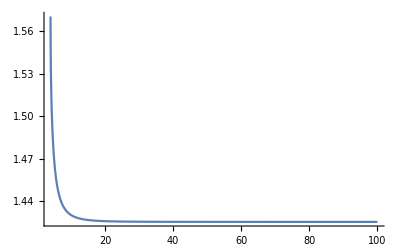

```mathematica
Plot[Evaluate[θ[r]/.Jointed],{r,r0j,100},PlotRange->All]
```

```mathematica
r0d=0.1;
DisJointed = NDSolve[{RHSr==LHSr,θ[r0d]==0.001,θ'[r0d]==100},θ[r],{r,r0d,100}];(*Solve for the solution which does cross from one side at θ=0 r =r0 *)
(*at small r0 expect this to be dominant solution*)
```

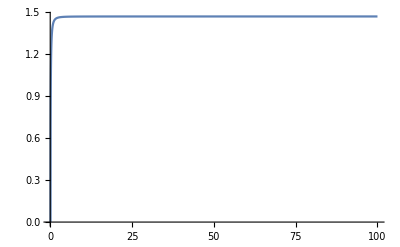

```mathematica
Plot[Evaluate[θ[r]/.DisJointed],{r,r0d,100},PlotRange->All]
```

```mathematica
beg=0.01;
end=1.0;
step=0.01;
Jsol= Table[NDSolve[{RHSr==LHSr,θ[r0]==Pi/2-0.0001,θ'[r0]==-100},θ[r],{r,r0,100},"ExtrapolationHandler"->{Indeterminate &}],{r0,beg,end,step} ];

Dsol = Table[NDSolve[{RHSr==LHSr,θ[r0]==0.01,θ'[r0]==100},θ[r],{r,r0,100},"ExtrapolationHandler"->{Indeterminate &}],{r0,beg,end,step}];
```

InterpolatingFunction::dmval: Input value {0.0000817143} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

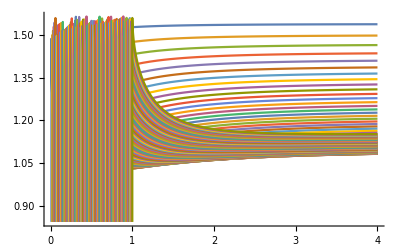

```mathematica
Plot[θ[r]/.Jsol,{r,0,4},Evaluated->True]
```

InterpolatingFunction::dmval: Input value {0.0000817143} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

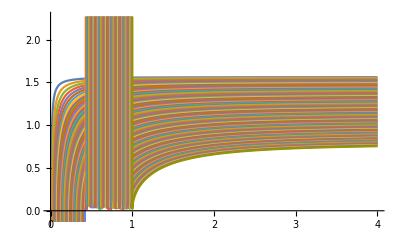

```mathematica
Plot[θ[r]/.Dsol,{r,0,4},Evaluated->True]
```

```mathematica
ActDisJoin = Table[Sqrt[(1/(1+(r^2)))+((r^2)*((Dt[θ[r]/.Dsol[[IntegerPart[(r0-beg+step)/step]]],r])^2))]*r*Sin[θ[r]/.Dsol[[IntegerPart[(r0-beg+step)/step]]]],{r0,beg,end,step}];
ActJoin = Table[Sqrt[(1/(1+(r^2)))+((r^2)*((Dt[θ[r]/.Jsol[[IntegerPart[(r0-beg+step)/step]]],r])^2))]*r*Sin[θ[r]/.Jsol[[IntegerPart[(r0-beg+step)/step]]]],{r0,beg,end,step}];
```

```mathematica
(*Do[(Print["=r0"r0];Print[Plot[{ActDisJoin[[IntegerPart[r0/step]]],ActJoin[[IntegerPart[r0/step]]],ActJoin[[IntegerPart[r0/step]]]-ActDisJoin[[IntegerPart[r0/step]]]},{r,r0,5},Evaluated->True,PlotLegends->"Expressions"]]),{r0,beg,end,step}]*)

(*at small r0, ie close to centre expecte disjointed solution to be energetically favourable, Δaction +ve.*)
(*at large r0, near boundary we expect joined solution to be favoured Δaction to be -ve*)

(*However, we actually see for small r0 (close to centre) we get the joined solution (seemingly a very thin soap bubble which extends very close to centre), then as we increase r0 (moving away from centre) Δ increases and we get the disjoined solution (like two disjointed soap bubbles forming near each pole)*)
```

```mathematica
Plot3D[{ActJoin[[IntegerPart[(r0-beg+step)/step]]],ActDisJoin[[IntegerPart[(r0-beg+step)/step]]]},{r0,beg,end},{r,r0,5},PlotLegends->{"ActionJoined","ActionDisJoined"},AxesLabel->Automatic,Axes->True]
```

InterpolatingFunction::dmval: Input value {0.0003575} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
Plot3D[{ActJoin[[IntegerPart[(r0-beg+step)/step]]]-ActDisJoin[[IntegerPart[(r0-beg+step)/step]]],r=0},{r0,beg,end},{r,r0,100},PlotLegends->{"ΔAction","r=0"},AxesLabel->Automatic,Axes->True, FaceGrids->All]
```

InterpolatingFunction::dmval: Input value {0.00715} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
Plot3D[{ActJoin[[IntegerPart[(r0-beg+step)/step]]]-ActDisJoin[[IntegerPart[(r0-beg+step)/step]]],r=0},{r0,0.5,0.55},{r,r0,100},PlotLegends->{"ΔAction","r=0"},AxesLabel->Automatic,Axes->{True,True,True},Ticks->Automatic,FaceGrids->All]
```

InterpolatingFunction::dmval: Input value {0.00715} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

-Graphics3D-